# 2. Finite thin tube: calculations ON axis

```mathematica
Clear["Global`*"];
```

```mathematica
(* physical parameters *)

a=0.05; (*radius of tube*)
h = 0.01;(*thickness of tube*)
(*h = a/3(1-(a/(a+h))^3)  (*effective thickness*)*)
H =0.5; (*length of tube*)
M = 0.0030; (* mass of the falling magnet*)
m = 2; (*dipole moment*)
σ=5.92 10^7; (*conductivity*)
μ =4π 10^-7; (*permeability*)
g = 9.81;
Y = 1/2; (* parameter giving distribution of current in ring body, Y=1/2 means uniform profile, more in  "Self inductance of a wire loop as a curve integral", R.Dengler, https://arxiv.org/pdf/1204.1486.pdf, I approximate the rectangular cross section of annular element of tube as circular cross section of a ring*)
γ = 20; (* decay constant of current, in units of s^-1 *)


(*simulation parameters*)

initHeight = 0.0 H;
tMax = 0.25;(*20*Sqrt[2(H+initHeight)/g]; in terms of time scale of free fall*)
n =10; (* number of partitions of the tube of length H *)
dζ = H/n; (* ζ is the general coordinate along tube axis from top opening, while z[t] denotes the position of magnet *) 
R = (2π a)/(σ h dζ); (*resistance of one elemental ring*)
selfInductanceRing = μ a (Log[(8a)/(h/2)]-2+Y/2) ;(*formula for quick calculation of self inductane of ring of cross section "radius" h/2 and main radius a *)
indices=Range[n];
getζ[index_]:=-(index-1/2)  dζ  (* get coordinate of centre of ring measured from top end of tube *)
J=ToExpression["J"<>ToString[#]]&/@Range[n];  (* store all curents Subscript[J, index] in list J, NB: J is not current density but standard current in Amperes! *)



(* calculation of mutual inductance of distant current loops *)
(*Mutual Inductance and Inductance Calculations by Maxwell’s Method, from Antonio Carlos M.de Queiroz: calcMutInd[Δζ_]:=Module[{k},k=(2a)/(√(4 a^2+Δζ^2)); -a μ((k-2/k)EllipticK[k]+2/k EllipticE[k])] 
but this gives nonsense result of increasing mutual inductance with distance!!!, below my custom derived formula*)
calcMutInd[Δζ_] := μ/2 NIntegrate[(ρ(a-ρ Cos[ϕ]))/((ρ^2+a^2+Δζ^2-2a ρ Cos[ϕ])^(3/2)),{ϕ,0,2π},{ρ,0,a}]
listΔζ =dζ*Range[0,n-1] (* all possible arrangements of two rings in our tube *)
mutInd = calcMutInd[listΔζ]  (* array whose entries correspond to mutual inductance of two rings in tube "index-1" dζ apart *)
(* this is important as it saves computational expense - no need to calculate inductances each iteration! *)
mutInd⟦1⟧=0;  (* treat the case of self-inductance of a single ring separately *)
mutInd

(* calculate tube-induced flux derivative for a given index: sum contributions from all other elements (and finally-itself)*)
(* getFluxDerFromTube[index_]:=0  *)
(*getFluxDerFromTube[index_]:=Total[  (calcMutInd[(index-#)dζ]J⟦#⟧'[t])&/@   (Drop[indices,{index}])    ]       +      selfInductanceRing*J⟦index⟧'[t] *)
getFluxDerFromTube[index_]:=Total[   ((mutInd⟦Abs[index-#]+1⟧)J⟦#⟧'[t])   &/@  (Drop[indices,{index}])    ]       +      selfInductanceRing*J⟦index⟧'[t] 

getFluxDerFromTube[1]

(* getFluxDerFromTube[index_]:=0 *)
```

{0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::inumri: The integrand (ρ (0.05-ρ Cos[ϕ]))/((0.0025+ρ^2-0.1 ρ Cos[ϕ])^(3/2)) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{6.2831853000627219072185358161479335468470319714384686449193395674,6.2831852975804563153282023466011913621562245957363757042912766337},{0.049999999475366399651913271615778367048480573808788562928384635598,«85»}}.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::inumri: The integrand (ρ (0.05-ρ Cos[ϕ]))/((0.0025+ρ^2-0.1 ρ Cos[ϕ])^(3/2)) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{6.2831853000627219072185358161479335468470319714384686449193395674,6.2831852975804563153282023466011913621562245957363757042912766337},{0.049999999475366399651913271615778367048480573808788562928384635598,«85»}}.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::inumri: The integrand (ρ (0.05-ρ Cos[ϕ]))/((0.0025+ρ^2-0.1 ρ Cos[ϕ])^(3/2)) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{6.2831853000627219072185358161479335468470319714384686449193395674,6.2831852975804563153282023466011913621562245957363757042912766337},{0.049999999475366399651913271615778367048480573808788562928384635598,«85»}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

{(π NIntegrate[(ρ (0.05-ρ Cos[ϕ]))/((0.0025+ρ^2-0.1 ρ Cos[ϕ])^(3/2)),{ϕ,0,2 π},{ρ,0,a}])/5000000,4.94078×10^-7,1.4186×10^-7,5.49625×10^-8,2.59984×10^-8,1.4106×10^-8,8.4376×10^-9,5.4236×10^-9,3.68299×10^-9,2.61114×10^-9}

{0,4.94078×10^-7,1.4186×10^-7,5.49625×10^-8,2.59984×10^-8,1.4106×10^-8,8.4376×10^-9,5.4236×10^-9,3.68299×10^-9,2.61114×10^-9}

1.65375×10^-7 J1'[t]+2.61114×10^-9 J10'[t]+4.94078×10^-7 J2'[t]+1.4186×10^-7 J3'[t]+5.49625×10^-8 J4'[t]+2.59984×10^-8 J5'[t]+1.4106×10^-8 J6'[t]+8.4376×10^-9 J7'[t]+5.4236×10^-9 J8'[t]+3.68299×10^-9 J9'[t]

```mathematica
(* calculation of magnetic force from many rings *)
(* properly summed magnetic force *)
getMagForce[z_]:=Total[   ((-3μ m a^2)/2(z-getζ[#])/((a^2+(z-getζ[#])^2)^(5/2))J⟦#⟧[t])&/@indices]


(* Solving the n+1 EoMs *)
EoMs = Flatten[{M z''[t]==-M g + getMagForce[z[t]], 
(R J⟦#⟧[t] == -(-3μ m a^2)/2((z[t]-getζ[#])z'[t])/((a^2+(z[t]-getζ[#])^2)^(5/2))- 10^-4 getFluxDerFromTube[#])&/@ indices }]
BCs= Flatten[{z[0]==initHeight,z'[0]==0,(#[0]==0)&/@J}]
(*
timeSol = Timing[NDSolve[Join[EoMs,BCs],Flatten[{z,J}],{t,0,tMax},Method->{"EquationSimplification"->"Residual"},MaxSteps->Infinity]]
timeTaken = timeSol[[1]]
sol = timeSol[[2]] *)

sol=NDSolve[Join[EoMs,BCs],Flatten[{z,J}],{t,0,tMax},Method->{"EquationSimplification"->"Residual"},MaxSteps->Infinity]
```

Total::normal: Nonatomic expression expected at position 1 in Total[indices].

{M z''[t]==-g M+Total[indices],indices}

{z[0]==initHeight,z'[0]==0,J}

NDSolve::deqn: Equation or list of equations expected instead of indices in the first argument {M z''[t]==-g M+Total[indices],indices,z[0]==initHeight,z'[0]==0,J}.

NDSolve[{M z''[t]==-g M+Total[indices],indices,z[0]==initHeight,z'[0]==0,J},{z,J},{t,0,tMax},Method→{EquationSimplification→Residual},MaxSteps→∞]

## Plot the results

Final position of magnet is -0.0197807

-Graphics-

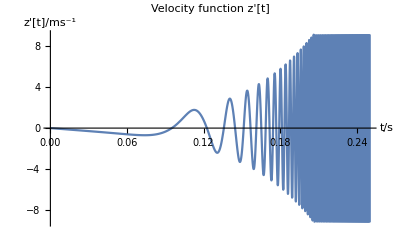

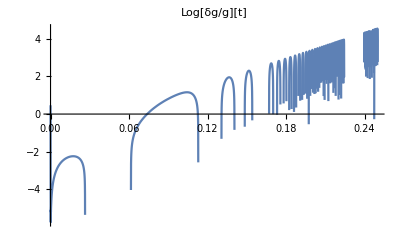

-Graphics-

```mathematica
pathIfn =sol[[1,1,2]];
pathIfn'[0.25];
currentsIfn = sol[[1,#,2]]&/@Range[2,n+1,1];

Print["Final position of magnet is "<>ToString[pathIfn[tMax]]]
Plot[{pathIfn[t],Callout[-H,"end of tube"],Callout[0,"beginning of tube"]},{t,0,tMax},PlotLabel->"Magnet displacement function z[t]",AxesLabel->{"t/s","z[t]/m"}]
Plot[pathIfn'[t],{t,0,1tMax},PlotLabel->"Velocity function z'[t]",AxesLabel->{"t/s","z'[t]/ms^-1"}]
Plot[pathIfn''[t],{t,0,tMax}, PlotRange->Full,AxesLabel->{"t/s","z''[t]/ms^-2"},PlotLabel->"Acceleration function"];
Plot[(g+pathIfn''[t])/g,{t,0,tMax}, PlotRange->All];
Plot[Log10[(g+pathIfn''[t])/g],{t,0,tMax}, PlotRange->All,PlotLabel->"Log[δg/g][t]"]

Show[Plot[Callout[currentsIfn⟦#⟧[t],"J"<>ToString[#],Bottom],{t,0,tMax}]&/@Range[1,n,n/5], PlotRange->All, PlotLabel->"Currents J_k[t] for selected k",AxesLabel->{"t/s","J_k[t]/A"}]

(*PlotRange->{-5 10^-6,+2 10^-6}*)
```

```mathematica
58028.01491491503
```

58028.

```mathematica
InterpolatingFunction[…]
```

InterpolatingFunction[…]

```mathematica
(* comparision of simulation results with experiments *)
M=0.003;
e = {1,2.1,3.1,4.1,5.8}; 

(* for 2a = 13.8 mm) *)
v={3.19,1.94,1.58,1.41,1.27}; (* in cm/s *)
k=100M g/v

(* for a = 9.5 mm *)
v = {14.30 ,6.174,4.871, 4.223, 3.657};
k = 100 M g / v

(* analysis of Donoso data *)
t8cm = {0.84, 1.47,1.67,1.83,1.87};
vDonoso = 0.08/t8cm ;
kDonoso = M g / vDonoso

myData = Partition[Riffle[e,k],2];
donosoData = Partition[Riffle[e,kDonoso],2];

myDataFn = Interpolation[myData];
donosoDataFn = Interpolation[donosoData];
Show[ListPlot[myData],ListPlot[donosoData],
Plot[Callout[myDataFn[e],"my sim. data"],{e,1,5.8},PlotStyle-> Orange],
Plot[ Callout[donosoDataFn[e], "Donoso exp. data"],{e,1,5.8}],PlotRange-> {{0,9},{0,1}},PlotLabel->"k/(N SuperscriptBox[m, -1] s) vs. wall thicknesse/mm" ]
```

{0.92163,1.51546,1.86076,2.08511,2.31496}

{0.205594,0.47619,0.603572,0.696188,0.803938}

{0.3087,0.540225,0.613725,0.672525,0.687225}

-Graphics-

```mathematica
Integrate[v^2/((1+v^2)^5),{v,-∞,+∞}]
```

(5 π)/128